```mathematica
FRZ10=0.2;
solidabv[iabv_,solidpc_]:=(iabv-FRZ10*(1-solidpc))/solidpc;
```

```mathematica
0.08/0.9 is (0.1-0.02)/0.9 is (i-FRZ10*(1-0.9))
```

```mathematica
solidabv[0.1,0.9]
```

0.0888889

```mathematica
solidabv[0.1,1]
```

0.1

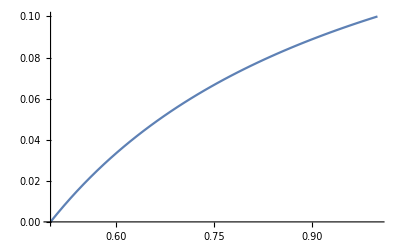

```mathematica
Plot[solidabv[0.1,x],{x,0.5,1}]
```